```mathematica
FF[n_] := Sum[ MoebiusMu[j](Log[j] - FF[n/j]),{j,2,n}]
```

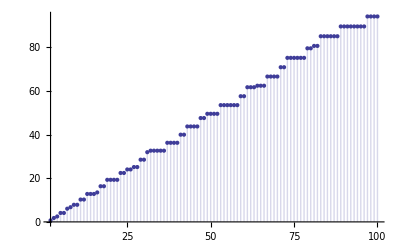

```mathematica
DiscretePlot[-FF[n],{n,2,100}]
```

```mathematica
FG[n_] := Sum[ MoebiusMu[j]^2(Log[j] - FG[n/j]),{j,2,n}]
```

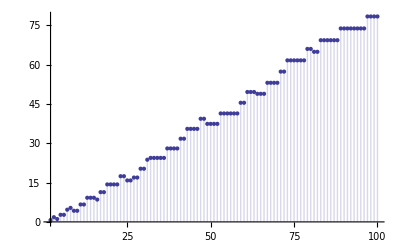

```mathematica
DiscretePlot[FG[n],{n,2,100}]
```

```mathematica
FH[n_] := Sum[LiouvilleLambda[j](Log[j] - FH[n/j]),{j,2,n}]
```

```mathematica
DiscretePlot[-FH[n],{n,2,100}]
```

-Graphics-

```mathematica
FI[n_, k_ ] := Sum[ MoebiusMu[ j ]^2( 1/k - FI[n/j, k+1] ), {j,2,n}]
```

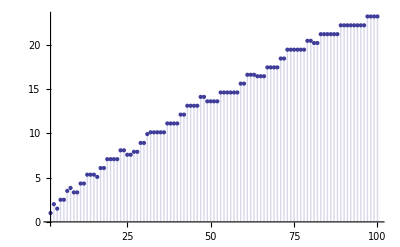

```mathematica
DiscretePlot[FI[n,1],{n,2,100}]
```

```mathematica
RR[n_,k_]:= RR[n,k] = Product[k/(FactorInteger[n][[j]][[2]]!),{j,1,Length[FactorInteger[n]]}]
RR[1,k_] := 1
```

```mathematica
RR[12,1]
```

1/2

```mathematica
FJ[n_, k_ ] := Sum[ RR[ j,1 ]( 1/k - FJ[n/j, k+1] ), {j,2,n}]
```

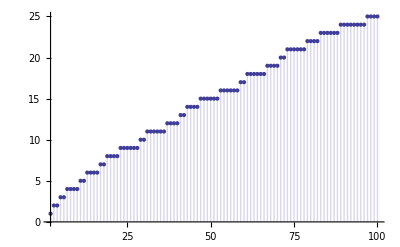

```mathematica
DiscretePlot[FJ[n,1],{n,2,100}]
```

```mathematica
FK[n_] := Sum[ RR[j,1](Log[j] - FK[n/j]),{j,2,n}]
```

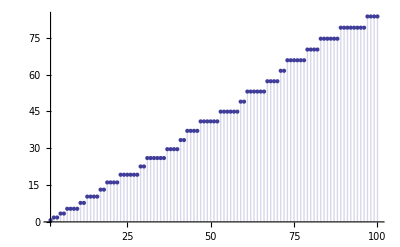

```mathematica
DiscretePlot[FK[n],{n,2,100}]
```

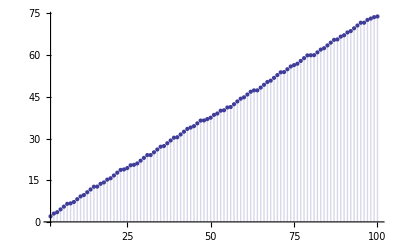

```mathematica
DiscretePlot[Sum[ RR[j,1],{j,1,n}],{n,2,100}]
```

```mathematica
FL[n_] := 1-Sum[ RR[j,1]FL[n/j],{j,2,n}]
```

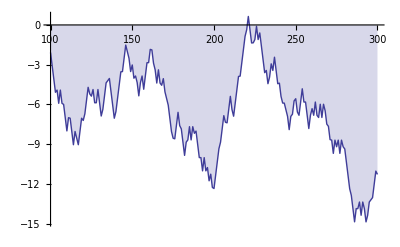

```mathematica
DiscretePlot[FL[n],{n,100,300}]
```

```mathematica
Table[ FL[n]-FL[n-1],{n,2,30}]
```

{-1,-1,1/2,-1,1,-1,-1/6,1/2,1,-1,-1/2,-1,1,1,1/24,-1,-1/2,-1,-1/2,1,1,-1,1/6,1/2,1,-1/6,-1/2,-1,-1}